#### BC_DirectPath_supp_3.nb Get data from BC_DirectPath (with Tmat = TmatBrownAn00) Sig1 and Sig2 need to be consistent with what you ran in BC_DirectPath.nb

```mathematica
PrintFigures=False;
```

```mathematica
mdir
odir=FileNameJoin[{mdir,"pdf_print"}]
otag=FileNameJoin[{odir,"DirectPath_supp_3"}]
```

```mathematica
SigCurve=TRIG;
SigCurve2=MONO;
```

```mathematica
Sig1
Sig2
Tmat1==Closest[Tmat,Sig1]
Tmat2==Closest[Tmat,Sig2]
```

```mathematica
dt
```

#### Check the beta for the peak of the discretized curve

```mathematica
betamax =Max[βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree&/@Ranget]
```

#### Round is necessary for Mathematica to recognize, for example, that 0.25 + 0.05 = 0.3

```mathematica
slope[t_]:=((βT[TT[Round[t+dt,.05],Tmat1,Tmat2],SigCurve]-βT[TT[t,Tmat1,Tmat2],SigCurve])/Degree)/dt;
```

#### Slope of each segment

```mathematica
MatrixNote[Tmat]
Ranget
dt
TableForm[Join[{{"   t","  βTRIG","  slope"}},{PaddedForm[#,{2,2}],PaddedForm[Round[βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree,.001],{4,3}],PaddedForm[slope[#],{5,2}]}&/@Ranget]]
```

#### Find the intersection between t = tt1 and t = tt2

```mathematica
tt1=.45;tt2=.65;
beta1=βT[TT[tt1,Tmat1,Tmat2],SigCurve]/Degree;
beta2=βT[TT[tt2,Tmat1,Tmat2],SigCurve]/Degree;
peak=({t,beta}/.Solve[(beta-beta1)/(t-tt1)==slope[tt1]&&(beta-beta2)/(t-tt2)==slope[tt2],{t,beta}])[[1]]
```

```mathematica
MatrixNote[Tmat]
Ranget
dt
plot=Graphics[{PointSize[.015],
Line[Sort[Join[{peak},{#,βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree}&/@Ranget]]],
{ColorData["Rainbow"][0/6],Point[{#,βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree}]&/@Ranget},
Point[{#,0}]&/@Ranget},Axes->True,AxesOrigin->{t1,0},AspectRatio->.5,ImageSize->500,Ticks->{Range[0,1,.2],Range[0,8,2]},TicksStyle->14]
```

#### The color range is specified at the top, and it should be adjusted based on the balls being shown (use Tmat2)

```mathematica
(*npts =10000;
AlphaMONOvalues=Sort[Table[Alpha[Tmat2,{RandomReal[{-π,π}],RandomReal[{0,π}]},MONO]/Degree,{k,npts}]];
Take[AlphaMONOvalues,5]
Take[AlphaMONOvalues,-5]*)
```

## Ball diagrams

```mathematica
eye=20xyztp[{60,65}];
AngRadDisk=2.Degree;
ShiftToEye=.06;
tkns=.01; (* tkns only affects XISO *)
```

```mathematica
cmin=0;cmax=18; dc=2;
contoursx=Range[cmin,cmax,dc];
MaxForScalingx=cmax-dc;
```

```mathematica
MatrixNote[Tmat]
contoursx
MaxForScalingx
PrintEye;
```

```mathematica
tIsPt2onBottom=Show[cpMONO[TT[.2,Tmat1,Tmat2],contoursx,MaxForScalingx, plotpoints, contourstyle],options]
tIsPt4onBottom=Show[cpMONO[TT[.4,Tmat1,Tmat2],contoursx,MaxForScalingx, plotpoints, contourstyle],options]
tIsPt6onBottom=Show[cpMONO[TT[.6,Tmat1,Tmat2],contoursx,MaxForScalingx, plotpoints, contourstyle],options]
tIsPt8onBottom=Show[cpMONO[TT[.8,Tmat1,Tmat2],contoursx,MaxForScalingx, plotpoints, contourstyle],options]
```

```mathematica
tIsPt2onTop=Show[{cpMONO[Closest[TT[.2,Tmat1,Tmat2],SigCurve],contoursx,MaxForScalingx, plotpoints, contourstyle],
Graphics3D[AllFoldGraphics[SigCurve,UT[TT[.2,Tmat1,Tmat2],SigCurve],ShiftToEye,eye]]},options]
tIsPt4onTop=Show[{cpMONO[Closest[TT[.4,Tmat1,Tmat2],SigCurve],contoursx,MaxForScalingx, plotpoints, contourstyle],
Graphics3D[AllFoldGraphics[SigCurve,UT[TT[.4,Tmat1,Tmat2],SigCurve],ShiftToEye,eye]]},options]
Ranget[[13]]
tIsPt6onTop=Show[{cpMONO[Closest[TT[Ranget[[13]],Tmat1,Tmat2],SigCurve],contoursx,MaxForScalingx, plotpoints, contourstyle],
Graphics3D[AllFoldGraphics[SigCurve,UT[TT[Ranget[[13]],Tmat1,Tmat2],SigCurve],ShiftToEye,eye]]},options]
tIsPt8onTop=Show[{cpMONO[Closest[TT[.8,Tmat1,Tmat2],SigCurve],contours,MaxForScalingx, plotpoints, contourstyle],
Graphics3D[AllFoldGraphics[SigCurve,UT[TT[.8,Tmat1,Tmat2],SigCurve],ShiftToEye,eye]]},options]
```

```mathematica
tIs1=Show[{cpMONO[Tmat2,contoursx,MaxForScalingx, plotpoints, contourstyle],
Graphics3D[AllFoldGraphics[Sig2,UT[Tmat,Sig2],ShiftToEye,eye]]},options]
tIs0=Show[{cpMONO[Tmat1,contoursx,MaxForScalingx, plotpoints, contourstyle],
Graphics3D[AllFoldGraphics[Sig1,UT[Tmat,Sig1],ShiftToEye,eye]]},options]
```

## Main plot

```mathematica
MatrixNote[Tmat]
Ranget
contoursx
MaxForScalingx
PrintEye;
dy=1.5betamax;  (* line segment *)
dyb=dy+0.;  (* ball *)
px=Graphics[{PointSize[.013],
 {PointSize[.001],Point/@{{.1,-3betamax},{.9,3.5betamax}}},  (* fake points - see also AspectRatio *)
{HueOfΣ[SigCurve],Line[Sort[Join[{peak},{#,βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree}&/@Ranget]]]},
{HueOfΣ[SigCurve],Point[{#,βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree}]&/@Ranget},
Line[{{Ranget[[#]],           βT[TT[Ranget[[#]],Tmat1,Tmat2],SigCurve]/Degree},
    {Ranget[[#]],dy+βT[TT[Ranget[[#]],Tmat1,Tmat2],SigCurve]/Degree}}]&/@{1,5,9,13,17,21},
Line[{{#,0},{#,-dy}}]&/@Range[0,1,.2],
Text[Style["(0, 0)",18],{-.05,0}],
Text[Style["(1, 0)",18],{1.05,0}],
Inset[tIsPt2onTop,{.2,dyb+βT[TT[.2,Tmat1,Tmat2],SigCurve]/Degree},Center,.18],
Inset[tIsPt4onTop,{.4,dyb+βT[TT[.4,Tmat1,Tmat2],SigCurve]/Degree},Center,.18],
Inset[tIsPt6onTop,{.6,dyb+βT[TT[Ranget[[13]],Tmat1,Tmat2],SigCurve]/Degree},Center,.18],
Inset[tIsPt8onTop,{.8,dyb+βT[TT[.8,Tmat1,Tmat2],SigCurve]/Degree},Center,.18],
Inset[tIs0,{0,dyb},Center,.18],,
Inset[tIs1,{1,dyb},Center,.18],
Inset[tIsPt2onBottom,{.2,-dyb},Center,.18],
Inset[tIsPt4onBottom,{.4,-dyb},Center,.18],
Inset[tIsPt6onBottom,{.6,-dyb},Center,.18],
Inset[tIsPt8onBottom,{.8,-dyb},Center,.18],
Inset[tIs0,{0,-dyb},Center,.18],
Inset[tIs1,{1,-dyb},Center,.18] ,
(* TRIV base curve *)
{HueOfΣ[TRIV],Line[{{0,0},{1,0}}]},
{HueOfΣ[TRIV],Point[{#,0}]&/@Ranget}
},Axes->False,AspectRatio->0.5,ImageSize->1000,PlotRange->All];
If[PrintFigures,Export[otag<>".pdf",px],px]
```

## Now add betaMONO

#### Ball diagrams

```mathematica
tIsPt2onTop2=Show[{cpMONO[Closest[TT[.2,Tmat1,Tmat2],SigCurve2],contoursx,MaxForScalingx, plotpoints, contourstyle],
Graphics3D[AllFoldGraphics[SigCurve2,UT[TT[.2,Tmat1,Tmat2],SigCurve2],ShiftToEye,eye]]},options]
tIsPt4onTop2=Show[{cpMONO[Closest[TT[.4,Tmat1,Tmat2],SigCurve2],contoursx,MaxForScalingx, plotpoints, contourstyle],
Graphics3D[AllFoldGraphics[SigCurve2,UT[TT[.4,Tmat1,Tmat2],SigCurve2],ShiftToEye,eye]]},options]
tIsPt6onTop2=Show[{cpMONO[Closest[TT[Ranget[[13]],Tmat1,Tmat2],SigCurve2],contoursx,MaxForScalingx, plotpoints, contourstyle],
Graphics3D[AllFoldGraphics[SigCurve2,UT[TT[Ranget[[13]],Tmat1,Tmat2],SigCurve2],ShiftToEye,eye]]},options]
tIsPt8onTop2=Show[{cpMONO[Closest[TT[.8,Tmat1,Tmat2],SigCurve2],contoursx,MaxForScalingx, plotpoints, contourstyle],
Graphics3D[AllFoldGraphics[SigCurve2,UT[TT[.8,Tmat1,Tmat2],SigCurve2],ShiftToEye,eye]]},options]
```

```mathematica
MatrixNote[Tmat]
Ranget
contoursx
MaxForScalingx
PrintEye;
dy=0.3betamax;  (* line segment *)
dyb=dy+0.;  (* ball *)
dy2=0;
dyb2=0;
px=Graphics[{PointSize[.013],
{PointSize[.001],Point/@{{.1,-.5betamax},{.9,1.5betamax}}}, (* fake points - see also AspectRatio *)
(* TRIG *)
{HueOfΣ[SigCurve],Line[Sort[Join[{peak},{#,βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree}&/@Ranget]]]},
{HueOfΣ[SigCurve],Point[{#,βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree}]&/@Ranget},
(* MONO *)
{HueOfΣ[SigCurve2],Line[{#,βT[TT[#,Tmat1,Tmat2],SigCurve2]/Degree}&/@Ranget]},
{HueOfΣ[SigCurve2],Point[{#,βT[TT[#,Tmat1,Tmat2],SigCurve2]/Degree}]&/@Ranget},
Line[{{#,0},{#,-dy}}]&/@Range[0,1,.2],
Line[{{Ranget[[#]],           βT[TT[Ranget[[#]],Tmat1,Tmat2],SigCurve]/Degree},
    {Ranget[[#]],dy+βT[TT[Ranget[[#]],Tmat1,Tmat2],SigCurve]/Degree}}]&/@{1,5,9,13,17,21},
Line[{{0,0},{1,0}}],
(*Text[Style["(0, 0)",18],{-.05,0}],*)
(*Text[Style["(1, 0)",18],{1.05,0}],*)
(* TRIV base curve *)
{HueOfΣ[TRIV],Line[{{0,0},{1,0}}]},
{HueOfΣ[TRIV],Point[{#,0}]&/@Ranget},
(* balls *)
Inset[tIsPt2onTop,{.2,dyb+βT[TT[.2,Tmat1,Tmat2],SigCurve]/Degree},Center,.18],
Inset[tIsPt4onTop,{.4,dyb+βT[TT[.4,Tmat1,Tmat2],SigCurve]/Degree},Center,.18],
Inset[tIsPt6onTop,{.6,dyb+βT[TT[Ranget[[13]],Tmat1,Tmat2],SigCurve]/Degree},Center,.18],
Inset[tIsPt8onTop,{.8,dyb+βT[TT[.8,Tmat1,Tmat2],SigCurve]/Degree},Center,.18],
Inset[tIs0,{0,dyb},Center,.18],
Inset[tIs1,{1,dyb},Center,.18],
Inset[tIsPt2onBottom,{.2,-dyb},Center,.18],
Inset[tIsPt4onBottom,{.4,-dyb},Center,.18],
Inset[tIsPt6onBottom,{.6,-dyb},Center,.18],
Inset[tIsPt8onBottom,{.8,-dyb},Center,.18],
Inset[tIs0,{0,-dyb},Center,.18],
Inset[tIs1,{1,-dyb},Center,.18] ,
(* MONO balls *)
Inset[tIsPt2onTop2,{.2,dyb2+βT[TT[.2,Tmat1,Tmat2],SigCurve2]/Degree},Center,.18],
Inset[tIsPt4onTop2,{.4,dyb2+βT[TT[.4,Tmat1,Tmat2],SigCurve2]/Degree},Center,.18],
Inset[tIsPt6onTop2,{.6,dyb2+βT[TT[Ranget[[13]],Tmat1,Tmat2],SigCurve2]/Degree},Center,.18],
Inset[tIsPt8onTop2,{.8,dyb2+βT[TT[.8,Tmat1,Tmat2],SigCurve2]/Degree},Center,.18]
},Axes->False,AspectRatio->0.8,ImageSize->1000,PlotRange->All];
If[PrintFigures,Export[otag<>"_three.pdf",px],px]
```

## Brown: dt = 0.05, Tmat1=TTRIG, Tmat2=TCUBE, ListSigma={MONO,TET,TRIG} [supp3]

#### From BC_Superlattice.nb (dt = 0.2) (There is no erroneous point on the MONO curve because the point is t = 0.7 whereas the discretization below is 0.2, 0.4, 0.6, 0.8.)

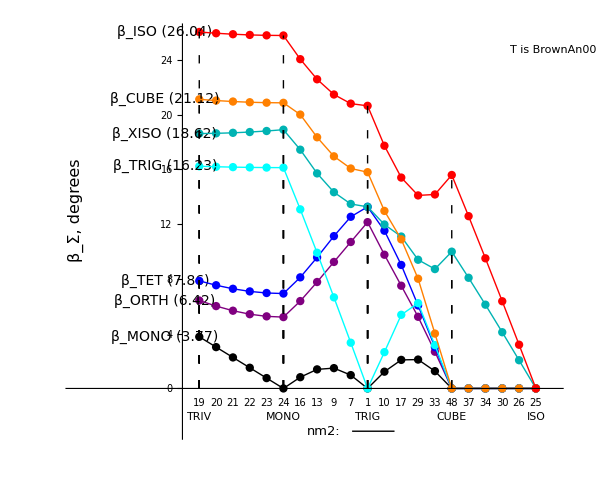

#### From BC_DirectPath.nb